## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/primary-repos/github/experiment-mathematica/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="rcs/fourier/latex/";  
Get["utility modules.m",Path->dirPack];
Get["rcs-tools-01.m",Path->dirnb<>"rcs/tools/"];
Get["plot-library-01.m",Path->dirnb<>"rcs/tools/"];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/ already exists.

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/ already exists.

CreateDirectory::filex: /Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/fourier/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.256662 GB

seed file: /Users/dantopa/primary-repos/github/experiment-mathematica/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: May 4, 2020, time: 01:56:39

nb: /Users/dantopa/primary-repos/github/experiment-mathematica/nb/rcs/fourier/latex/singles-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.256662 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,5},{Automatic,5}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

#### tagger

```mathematica
Clear[tagSource];
tagSource[str_OutputStream,comment_String]:=Module[{},
(* tag Mathematica file *)
Write[str,comment,nb];
Write[str,comment,dirHome];
mark;
Write[str,comment,"user: ",user,", CPU: ",CPU,", MM v. ",mmv];
Write[str,comment,time," ",date];
Write[str,""];
]
```

## import rcs

```mathematica
σ=Import[dirDataLocker<>sciaccarcs];
Dimensions[σ]
λ=Length[σ]
```

{28,361}

28

## test case

### inherited from MoM

```mathematica
mesh=Range[-180,180];
```

### example

```mathematica
nu=25;
d=46;
knu=nu-2;
b=σ[[knu]];
```

### compute

```mathematica
fileName="nu="<>ToString[nu]<>"-d="<>pad[d];
(* build linear system *)
A=BuildAFourierCos[mesh,d];
(* least squares solution *)
x=LeastSquares[A,b];
(* error analysis *)
```

```mathematica
{errs,sn}=errorN[A,x,b];
```

## plot

```mathematica
g001=plotDatavFit[x,b,mesh]
```

plotDatavFit[8,{27.769,27.4725,26.5065,25.0035,23.1655,21.2347,19.4553,18.023,17.0066,16.2815,15.5818,14.6711,13.4798,12.1808,11.3276,11.3398,11.6355,11.7576,11.5583,11.019,10.196,9.19917,8.17262,7.26252,6.58365,6.32104,7.86002,10.313,12.9223,15.4717,17.749,19.5457,20.6614,20.93,20.2648,18.6736,16.2626,13.2337,9.87862,6.57341,5.49848,6.26705,7.37482,8.41303,9.21859,9.95597,10.8306,11.8121,12.7045,13.3174,13.6104,13.6135,13.8096,13.6792,12.7358,11.0209,8.7895,6.58263,5.34537,6.16325,7.40541,8.21022,8.50277,8.5088,8.6439,9.2171,10.1558,11.136,11.8052,11.8946,11.3024,10.1997,8.88959,7.49652,6.30227,6.74873,9.19403,11.3133,12.301,11.8337,9.84227,6.77922,5.44348,10.1241,17.505,25.5345,33.3696,40.33,45.8347,49.44,50.8409,49.8704,46.5777,41.2494,34.3742,26.586,18.5921,11.1016,4.89676,3.36374,5.55162,7.32929,8.03998,8.0849,7.91059,7.82933,8.06072,8.34709,8.37935,8.09347,7.94612,8.64994,9.96993,11.2406,12.0899,12.3607,12.0305,11.1873,10.0357,8.96123,8.38286,8.13995,7.94389,7.65599,7.245,6.7845,6.41186,6.26707,6.45209,6.95922,7.64392,8.37349,9.1173,9.88053,10.6063,11.1721,11.459,11.411,11.0752,10.6617,10.693,11.625,13.0371,14.5077,15.7884,16.6845,17.0482,16.7944,15.9083,14.444,12.5157,10.2854,7.95456,5.77645,4.1145,3.4814,4.11773,5.25803,6.35883,7.24901,7.85417,8.12595,8.0338,7.60131,8.28021,10.7498,13.3379,15.8052,17.9326,19.5107,20.3685,20.4014,19.593,18.0256,15.8755,13.3988,10.9712,11.0751,12.7814,13.941,14.3355,13.9038,12.7117,11.0194,11.2538,13.665,16.0912,18.1596,19.617,20.2926,20.1122,19.1018,17.3768,15.1196,12.5494,9.88914,7.33674,7.37707,7.86123,7.96673,7.71321,7.14015,6.29391,5.23436,4.10026,3.33106,3.68825,5.2624,7.46547,9.86464,12.1897,14.227,15.8002,16.7806,17.1019,16.7717,15.8742,14.5635,13.0458,11.5726,10.5247,10.3309,10.6468,10.9107,10.8898,10.6369,10.0888,9.41339,8.78399,8.2485,7.73914,7.23675,6.85472,6.73849,6.89938,7.22142,7.65061,7.99675,8.1473,8.15784,8.20284,8.6267,9.70096,10.9644,11.9689,12.4673,12.3335,11.5607,10.2909,8.88935,8.03161,8.08206,8.39255,8.43094,8.21537,8.00717,7.88594,7.7877,7.58014,6.90286,5.34074,3.41092,4.60052,10.6019,17.9475,25.8628,33.6372,40.5576,45.9823,49.4356,50.6751,49.5223,46.0366,40.5282,33.4894,25.54,17.3859,9.87503,5.0341,6.42293,9.58304,11.6355,12.1747,11.3076,9.39002,7.25724,6.87537,8.0056,9.34819,10.5577,11.5002,11.9634,11.8146,11.1307,10.1286,9.10712,8.38314,8.0951,7.99864,7.68742,6.93458,5.84419,5.31765,6.71395,8.92862,11.0555,12.6806,13.5678,13.6911,13.5697,13.6474,13.3994,12.7208,11.7352,10.6458,9.66098,8.84087,7.99441,6.94123,5.83571,5.12482,6.45742,9.66709,12.9547,15.9321,18.3136,19.8997,20.5828,20.3482,19.269,17.492,15.2145,12.6588,10.0453,7.59335,6.21766,6.51869,7.17052,8.04677,9.04849,10.0353,10.8587,11.3987,11.5849,11.4141,10.9947,10.8747,12.0387,13.5434,14.7774,15.6171,16.1608,16.6987,17.5718,18.9458,20.7418,22.7363,24.6635,26.2708,27.3518,27.769},{-180,-179,-178,-177,-176,-175,-174,-173,-172,-171,-170,-169,-168,-167,-166,-165,-164,-163,-162,-161,-160,-159,-158,-157,-156,-155,-154,-153,-152,-151,-150,-149,-148,-147,-146,-145,-144,-143,-142,-141,-140,-139,-138,-137,-136,-135,-134,-133,-132,-131,-130,-129,-128,-127,-126,-125,-124,-123,-122,-121,-120,-119,-118,-117,-116,-115,-114,-113,-112,-111,-110,-109,-108,-107,-106,-105,-104,-103,-102,-101,-100,-99,-98,-97,-96,-95,-94,-93,-92,-91,-90,-89,-88,-87,-86,-85,-84,-83,-82,-81,-80,-79,-78,-77,-76,-75,-74,-73,-72,-71,-70,-69,-68,-67,-66,-65,-64,-63,-62,-61,-60,-59,-58,-57,-56,-55,-54,-53,-52,-51,-50,-49,-48,-47,-46,-45,-44,-43,-42,-41,-40,-39,-38,-37,-36,-35,-34,-33,-32,-31,-30,-29,-28,-27,-26,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180}]

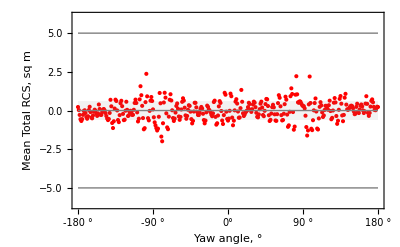

```mathematica
g002=plotScatterResidualN[residual,mesh,5]
```

```mathematica
createTicks["a",d,2];
ticksA;
```

```mathematica
ebars=createErrorBars[x,errs];
```

```mathematica
g003=plotBarAmplitudes[ebars,ticksA];
```

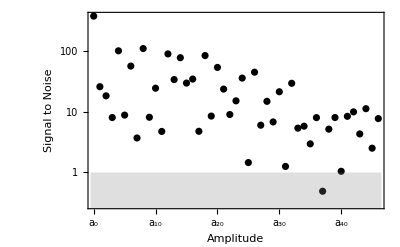

```mathematica
g004=plotSignalToNoise[sn,d,ticksB]
```

```mathematica
ζ=Import["/Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/fourier/search/data/norms/norm-inf-05.dat","Data"]
```

{{25.6306},{21.3073},{18.728},{14.9538},{3.55818},{2.19633},{2.06582},{1.14928},{0.775619},{0.631965},{0.573416},{0.555908},{0.627625},{0.474788},{0.476057},{0.476264},{0.501472},{0.42163},{0.420619},{0.432475},{0.43865},{0.403035},{0.408448},{0.412192},{0.411577},{0.396639},{0.410552},{0.408242},{0.405121},{0.391941},{0.400872},{0.396877},{0.390633},{0.383364},{0.397458},{0.393313},{0.385973},{0.381966},{0.39134},{0.388237},{0.380823},{0.381382},{0.389789},{0.387846},{0.379338},{0.379414},{0.382677},{0.381484},{0.374362},{0.377027},{0.377968}}

```mathematica
First[#]&/@ζ
```

{25.6306,21.3073,18.728,14.9538,3.55818,2.19633,2.06582,1.14928,0.775619,0.631965,0.573416,0.555908,0.627625,0.474788,0.476057,0.476264,0.501472,0.42163,0.420619,0.432475,0.43865,0.403035,0.408448,0.412192,0.411577,0.396639,0.410552,0.408242,0.405121,0.391941,0.400872,0.396877,0.390633,0.383364,0.397458,0.393313,0.385973,0.381966,0.39134,0.388237,0.380823,0.381382,0.389789,0.387846,0.379338,0.379414,0.382677,0.381484,0.374362,0.377027,0.377968}

```mathematica
First[ζ[[11]]]
Head[%]
```

0.573416

Real

```mathematica
Clear[errorSpectra];
errorSpectra[ν_Integer,dof_Integer]:=Module[{stub},
stub="/Users/dantopa/primary-repos/github/experiment-mathematica/io/rcs/fourier/search/data/norms/";
index=ToString[pad[ν]];
(* harvest data *)
ζ=Import[stub<>"norm-two-"<>index<>".dat","Data"];
two=First[#]&/@ζ;
ζ=Import[stub<>"norm-inf-"<>index<>".dat","Data"];
inf=First[#]&/@ζ;
(* inf norm *)
lblx="Degree of fit";
lbly="Infinity Norm Error";
ga=ListLogPlot[{Range[0,50],inf}ᵀ,
PlotStyle->Black,
Frame->True];
x=dof;
y=Log[inf[[dof]]];
hline=Line[{{-1,y},{51,y}}];
vline=Line[{{x-1,Log[0.0001]},{x-1,Log[100000]}}];
gb=Graphics[{Gray,Opacity[0.5],hline,vline}];
ginf=Show[{ga,gb},ipad,FrameLabel->{lblx,lbly}];
(* inf norm *)
lbly="2-Norm Error";
ga=ListLogPlot[{Range[0,50],two}ᵀ,
PlotStyle->Black,
Frame->True];
x=dof;
y=Log[two[[dof]]];
hline=Line[{{-1,y},{51,y}}];
vline=Line[{{x-1,Log[0.0001]},{x-1,Log[100000]}}];
gb=Graphics[{Gray,Opacity[0.5],hline,vline}];
gtwo=Show[{ga,gb},ipad,FrameLabel->{lblx,lbly}];
]
```

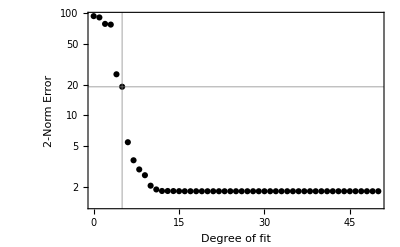

{92.9949,90.3045,78.1311,76.9045,25.2059,19.0607,5.48548,3.65811,2.978,2.61621,2.068,1.90062,1.83561,1.83545,1.83321,1.82899,1.82652,1.826,1.82599,1.82596,1.82588,1.82584,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82582,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581,1.82581}

{9.772,8.44916,9.19368,8.166,2.99477,1.90035,0.793732,0.489833,0.434097,0.367062,0.284021,0.250582,0.216108,0.214596,0.215721,0.211362,0.204673,0.202052,0.202062,0.201435,0.201429,0.201027,0.201112,0.201208,0.201193,0.201281,0.20129,0.201296,0.201343,0.201368,0.201412,0.201394,0.20132,0.201304,0.201318,0.201334,0.201368,0.201367,0.201336,0.20132,0.201315,0.201327,0.201352,0.201358,0.201345,0.201329,0.201319,0.201325,0.20134,0.20135,0.201347}

```mathematica
errorSpectra[3,6];
gtwo
two
inf
```

Line[{{-1,-0.713691},{51,-0.713691}}]

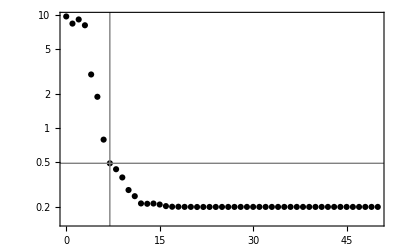

```mathematica
ga=ListLogPlot[{Range[0,50],inf}ᵀ,
PlotStyle->Black,
Frame->True];
x=8;
y=Log[inf[[x]]];
hline=Line[{{-1,y},{51,y}}]
vline=Line[{{x-1,Log[0.0001]},{x-1,Log[100]}}];
gb=Graphics[{Gray,hline,vline}];
ginf=Show[{ga,gb},ipad]
```

## significant digits

```mathematica
Clear[significantDigits];
significantDigits[x_,σ_]:=Module[{},
(* find power *)
lg=Log[10,σ];
power=Abs[Floor[lg]+Sign[lg]];
y=Round[10^power x];
id=IntegerDigits[y];
dec=Take[id,-power];
dig=(y/10^power)//N;
If[dig<0,Return[ToString[dig]]];
(* easy part: integer *)
ip=IntegerPart[x];
sip=ToString[ip];
(* hard part: fractional *)
sfp="";
Do[
sfp=sfp<>ToString[dec[[k]]];
,{k,power}];
Return[sip<>"."<>sfp];
]
significantDigits[x[[2]],errs[[1]]]
dec
```

-1.6454

{6,4,5,4}

## build function

```mathematica
Clear[mybasis];
mybasis[x_List,α_]:=Table[
Cos[k α]
,{k,0,Length[x]-1}]
```

```mathematica
mybasis[x,α]
```

{1,Cos[α],Cos[2 α],Cos[3 α],Cos[4 α],Cos[5 α],Cos[6 α],Cos[7 α],Cos[8 α],Cos[9 α],Cos[10 α],Cos[11 α],Cos[12 α]}

```mathematica
tbl=Table[
significantDigits[x[[k]],errs[[k]]]
,{k,Length[x]}]
```

Take::take: Cannot take positions -4 through -1 in {6,0,8}.

Take::take: Cannot take positions -4 through -1 in {3,6,6}.

{35.2416,-1.6454,-3.3896,1.0544,5.4009,1.2326,1.3577,0.3048,0.1579,-0.1063,-0.1193,-0.0608,-0.0366}

```mathematica
Clear[myfunction];
myfunction[tbl_]:=Module[{λ},
λ=Length[tbl];
fcn="f_{~nu}(~alpha) = "<>tbl[[1]];
Do[
num=tbl[[k]];
sgn=" + ";
If[StringTake[num,1]=="-",sgn=" - ";num=StringDrop[num,1]];
If[k==2,freq="",freq=ToString[k-1]];
term=sgn<>num<>" ~cos("<>freq<>"~alpha)";
fcn=fcn<>term;
,{k,2,λ}];
(* fcn=StringReplace[fcn,"~"->FromCharacterCode[92]]; *)
Return[fcn];
];
```

```mathematica
myfunction[tbl]
```

f_{~nu}(~alpha) = 35.2416 - 1.6454 ~cos(~alpha) - 3.3896 ~cos(2~alpha) + 1.0544 ~cos(3~alpha) + 5.4009 ~cos(4~alpha) + 1.2326 ~cos(5~alpha) + 1.3577 ~cos(6~alpha) + 0.3048 ~cos(7~alpha) + 0.1579 ~cos(8~alpha) - 0.1063 ~cos(9~alpha) - 0.1193 ~cos(10~alpha) - 0.0608 ~cos(11~alpha) - 0.0366 ~cos(12~alpha)

```mathematica
ζ=Import[dirData<>"sweep-te.dat","Data"];
Head[%]
```

List

```mathematica
ζ[[1,2]]
```

23664.01409902447,

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```